```mathematica
(*V30.0*) (*"Ryddet op"*)
```

```mathematica
Quit
```

```mathematica
DotOptimization[UnEditedbillede_, pixels_,ED_,lag_]:=Module[
{billede,LayerPixels,AllLayers,kmax=lag,deltadepth,v,c,k,i,o,GrayLayer,antal,n,p,layer,SignLayer,LayerSelect,xOfset, yOfset, Scaling,l1,l2,l3,l4, depth,length,edge,EdgeLayer,GrayLayers,størsteX,sign,størsteY},

billede = ImageResize[UnEditedbillede,pixels];
LayerSelect=0.1;

edge=PixelValuePositions[Thinning[EdgeDetect[ImageResize[billede,ED],0.5]],1]; (* edgedetect lag*)
(* Scaling = 91.92388155425118/Max[First[Transpose[edge]]], og ( edge[[i,1]]-xOfset)*Scaling. Vi starter med at trække offset fra alle punkter i x retningen, så billedet bliver rykket halvdelen af den maksimale x værdi mod venstre. Dette centrerer billedet omkring y aksen. (gentages for y).Scaling svarer til XmaksTegning/XmaksBillede, dvs. vi ender med xny/xmaksbillede*xmakstegning -> vi tager forholdet mellem den nye xværdi og den maksimale xværdi og ganger den med vores maksimale x for vores tegning(gentages for y) *)
xOfset = N[Max[First[Transpose[PixelValuePositions[ImageResize[billede,ED],Black,1]]]]/2];(*samme offset i hele billede*)(* offset er halvdelen af den maksimale x eller y værdi*)
yOfset =N[Max[Last[Transpose[PixelValuePositions[ImageResize[billede,ED],Black,1]]]]/2];

If[xOfset>yOfset, Scaling = 91.92388155425118/(2*xOfset), Scaling=91.92388155425118/(2*yOfset) ];
(* vi skal vælger hvilken akse vi scaler baseret på hele billedet så edge og layers ikke strækker forskelligt*)
(*Ofset x-koordinat*)
For[i = 1, i ≤ Length[edge], i++,edge[[i,1]]=( edge[[i,1]]-xOfset)*Scaling];
(*Ofset y-koordinat*)
For[i = 1, i ≤ Length[edge], i++,edge[[i,2]]=( edge[[i,2]]-yOfset )*Scaling];(* disse 2 kommandoer finder shortest tour i vores liste og kalder denne nye liste EdgeLayer*)
EdgeLayer=edge[[Last[FindShortestTour[edge]]]];
sign=PixelValuePositions[ImageResize[-Graphics-,500],Black];
xOfset = N[1/2 Max[First[Transpose[sign]]]];
yOfset =N[Max[Last[Transpose[sign]]]/2];
 Scaling=91.92388155425118/(2*xOfset) ;
For[i = 1, i ≤ Length[sign], i++,sign[[i,1]]=( sign[[i,1]]-xOfset)*Scaling];
For[i = 1, i ≤ Length[sign], i++,sign[[i,2]]=( sign[[i,2]]-12*yOfset )*Scaling];
SignLayer=sign[[Last[FindShortestTour[sign]]]];

(*edgelayer har andet offset end resten, da pixels er 100*)
xOfset = N[Max[First[Transpose[PixelValuePositions[billede,Black,1]]]]/2];
yOfset =N[Max[Last[Transpose[PixelValuePositions[billede,Black,1]]]]/2];
If[xOfset>yOfset, Scaling = 91.92388155425118/(2*xOfset), Scaling=91.92388155425118/(2*yOfset) ];
Print["Edge Slut"];
deltadepth=6/kmax;
k=0; 
GrayLayer={};
AllLayers={};

EdgeLayer = Join[Map[Append[#,-kmax*deltadepth]&,SignLayer],Map[Append[#,-kmax*deltadepth-2]&,EdgeLayer]];


Print["Edge depth slut"];
While [kmax≥  k,(* loopet stopper når k+1= kmaks, dvs at l2 bliver PVP for n=0.9 *)
If[k==0,layer=0,layer=LayerSelect+(k-1)*(0.9-LayerSelect)/kmax];(*hvis k=-1 går vi fra 0 til layerselect(ideel n) *)
l1=PixelValuePositions[ColorConvert[billede,GrayLevel],Black,layer];
l2=PixelValuePositions[ColorConvert[billede,GrayLevel],Black,LayerSelect+k*(0.9-LayerSelect)/kmax];
l2=Complement[l2,l1];(*fjerner alle værdier i l1 fra l2, dvs vi får kun de pixels på l2 der lægges til mellem n i l1 og n i l2*)
Print["lag:"ToString[k]];
Print["complement slut, difflist genereret"];
If[Length[l2]==0,GrayLayer={},(*hvis l2 ikke har værdier, lægges der ikke pixels til, og laget bliver ingenting*)
If[k≥1,
p=kmax-k+5;
i=1;
While[i≤ k,
l2=Drop[l2,{1,Length[l2],p}];
i+=1],
{}];
Print["udtynding af liste slut"];
(*Ofset x-koordinat*)
For[i = 1, i ≤ Length[l2], i++,l2[[i,1]]=( l2[[i,1]]-xOfset)*Scaling];
(*Ofset y-koordinat*)
For[i = 1, i ≤ Length[l2], i++,l2[[i,2]]=( l2[[i,2]]-yOfset )*Scaling];
Print["scaling slut"];
GrayLayer=l2[[Last[FindShortestTour[l2]]]]; 
depth=-(kmax-k)*deltadepth;(*udregner tegnedybden for vores lag, starter med deltadepth*kmax og slutter på 0 for det lyseste lag *)

GrayLayer = Map[Append[#,depth]&,GrayLayer]; (*ligger tegnedybde ind som sidste koordinat i vores lag*)
Print["Depth added"];
AllLayers=Join[AllLayers,GrayLayer](*ligger lag til vores samlede liste*)
];
k+=1;
];
Print["Udskriver data som liste"];
Join[AllLayers,EdgeLayer]
]
```

```mathematica
gkode[l_]:=Module[{lg,h,i,p,g,k,s,s0,s1,s2,s3,s4,s5,s6,s7,s8,j,z,ld,L,Lsidst,slid1,proc,zspidser,x,zbase,zdybest, AntalSpidsninger, Loops},
AntalSpidsninger = 0;
i=2;(* tager ikke første punkt*)
lg={};
ld={};
Loops=0;
zspidser=0;
zdybest=Min[Last[Transpose[l]]];(* udregner laveste z værdi*)
j=-1;(*vores skridtcounter for bevægelser i blyantspidsning*)
While [i≤ Length[l],
Loops+=1;(* tæller antal totale gennemløbninger og printer den hvert 10000 loop*)
If[Loops≥ 10000,Print[ToString[i-1]]; Loops=0];
k=i+j;
L=EuclideanDistance[l[[i]],l[[i-1]]];(*hvis i>1 udregner vi L=distance mellem 2 punkter, og bestemmer om det er en luft eller tegnebevægelse udfra om afstanden mellem 2 punkter er >sqrt(2)*)
zbase=l[[i,3]];
If[L<N[Sqrt[2]],g="01",If[zbase==zdybest&&L<N[Sqrt[10]],g="01",g="00"]]; (*bestemmer g00 eller g01*)
If[g=="01",ld=Insert[ld,L,-1]];(* hvis g er en tegnebevægels indsætter vi bevægelsens distance på liste med distance bevæget for hvert skridt*)
(*startværdien for z tages fra listen l*)
slid1=4*10^-13 x^3-3*10^-8 x^2+0.0006x+0.2137;(*1. slidfunktion*)
If[g=="01",(*hvis i≥2 og en tegnebevægelse, udregnes differensen i højden ved at indsætte den totale bevægelsesdistance i slidformlen*)(* which til flere muligheder for z kan addes *)
h=slid1/.{x->Total[ld]};
z=zbase-h-zspidser,z=5];
(* vores z værdi er baseværdien minus den højde h af blyanten der er slidt væk minus den mængde blyant vi har mistet ved spidsninger*)
If[h>2.5||((l[[i-1,3]]≠ l[[i,3]])&&l[[i,3]]==zdybest),(*aktiverer spidsning over h 3.5*)
s="Spidsning nr: H , J%";
AntalSpidsninger+=1;
proc=NumberForm[N[i/(Length[l]+j),3]*100,3];
s=StringReplace[s,{"H"->ToString[AntalSpidsninger],"J"->ToString[proc]}];
Print[ToString[s]];
s="NK G98 ZV";
s=StringReplace[s,{"K"->ToString[k],"V"->ToString[-zspidser-h-40]}]; (*indsætter spidsebevægelse*)
lg=Insert[lg,s,-1];
ld={0};(*ld sættes til slid ved kanttegning *)
zspidser+=0.5; (*zspidser juster z værdi ned for hver spidsning*)
s0="NK G00 XH YJ Z5";
s0=StringReplace[s0,{"K"->ToString[k+1],"H"->ToString[l[[i]][[1]]],"J"->ToString[l[[i]][[2]]]}];
s1="NK G00 X50 Y-50 Z5";
s1=StringReplace[s1,{"K"->ToString[k+2]}];
s2="NK G01 X50 Y-50 ZV";
s2=StringReplace[s2,{"K"->ToString[k+3],"V"->ToString[-zspidser-8]}];
s3="NK G01 X50 Y50 ZV";
s3=StringReplace[s3,{"K"->ToString[k+4],"V"->ToString[-zspidser-8]}];
s4="NK G01 X-50 Y50 ZV";
s4=StringReplace[s4,{"K"->ToString[k+5],"V"->ToString[-zspidser-8]}];
s5="NK G01 X-50 Y-50 ZV";
s5=StringReplace[s5,{"K"->ToString[k+6],"V"->ToString[-zspidser-8]}];
s6="NK G01 X50 Y-50 ZV";
s6=StringReplace[s6,{"K"->ToString[k+7],"V"->ToString[-zspidser-8]}];
s7="NK G00 X50 Y-50 Z5";
s7=StringReplace[s7,{"K"->ToString[k+8]}];
s8="NK G00 XH YJ Z5";
s8=StringReplace[s8,{"K"->ToString[k+9],"H"->ToString[l[[i+1]][[1]]],"J"->ToString[l[[i+1]][[2]]]}];
lg=Insert[lg,s0,-1];
lg=Insert[lg,s1,-1];lg=Insert[lg,s2,-1];lg=Insert[lg,s3,-1];lg=Insert[lg,s4,-1];lg=Insert[lg,s5,-1];lg=Insert[lg,s6,-1];
lg=Insert[lg,s7,-1];
lg=Insert[lg,s8,-1];
(*9 strings laver slidfirkant efter spidsning, j øges med 9 fordi blyantspidsningen laver 6 Gkode linjer. Da k er en sum at i og j, øges Nk med den korrekte mængde, men i øges kun med 1. dette gør at vi ikke springer punkter over*)
h=0;
j+=9;
,
s="NK GL XH YJ ZV";
If[g=="01",
s=StringReplace[s,{"K"->ToString[k],"L"->ToString[g],"H"->ToString[l[[i]][[1]]],"J"->ToString[l[[i]][[2]]],"V"->ToString[z]}];
lg=Insert[lg,s,-1],
(* vores standard gkode kommando, indsætter k som nummer, luft eller tegnebevægelse, z fra udregningen før, og x og y fra listen*)
s="NK GL XH YJ ZV";
s=StringReplace[s,{"K"->ToString[k],"L"->ToString[g],"H"->ToString[l[[i-1]][[1]]],"J"->ToString[l[[i-1]][[2]]],"V"->ToString[z]}];
lg=Insert[lg,s,-1];
s="NK GL XH YJ ZV";
s=StringReplace[s,{"K"->ToString[k+1],"L"->ToString[g],"H"->ToString[l[[i]][[1]]],"J"->ToString[l[[i]][[2]]],"V"->ToString[z]}];
lg=Insert[lg,s,-1];
j+=1]
];
i+=1
];
s="NK G98 ZV";
s=StringReplace[s,{"K"->ToString[k],"V"->ToString[-zspidser-h-40]}];
lg=Insert[lg,s,-1];
s0="NK G00 XH YJ Z5";
s0=StringReplace[s0,{"K"->ToString[k+1],"H"->ToString[l[[i-1]][[1]]],"J"->ToString[l[[i-1]][[2]]]}];
s1="NK G00 X50 Y-50 Z5";
s1=StringReplace[s1,{"K"->ToString[k+2]}];
s2="NK G01 X50 Y-50 ZV";
s2=StringReplace[s2,{"K"->ToString[k+3],"V"->ToString[-zspidser-8]}];
s3="NK G01 X50 Y50 ZV";
s3=StringReplace[s3,{"K"->ToString[k+4],"V"->ToString[-zspidser-8]}];
s4="NK G01 X-50 Y50 ZV";
s4=StringReplace[s4,{"K"->ToString[k+5],"V"->ToString[-zspidser-8]}];
s5="NK G01 X-50 Y-50 ZV";
s5=StringReplace[s5,{"K"->ToString[k+6],"V"->ToString[-zspidser-8]}];
s6="NK G01 X50 Y-50 ZV";
s6=StringReplace[s6,{"K"->ToString[k+7],"V"->ToString[-zspidser-8]}];
lg=Insert[lg,s0,-1];
lg=Insert[lg,s1,-1];lg=Insert[lg,s2,-1];lg=Insert[lg,s3,-1];lg=Insert[lg,s4,-1];lg=Insert[lg,s5,-1];(* laver tegnebevægelse til sidst så vi slider blyant lidt og er klar til at starte med nyt billede*)
lg
]


(*C:\Users\Peter\Desktop\\gkode_tiger.nc*)
```

```mathematica
-Graphics-,-Graphics-,-Graphics-,-Graphics-
```

```mathematica
Export["C:\\Users\\Philip\\Desktop\\gkodetest.nc",
Flatten[gkode[DotOptimization[-Graphics-,300,200,6]]],"Text"]
```

Edge Slut

Edge depth slut

0 lag:

complement slut, difflist genereret

udtynding af liste slut

scaling slut

Depth added

1 lag:

complement slut, difflist genereret

udtynding af liste slut

scaling slut

Depth added

2 lag:

complement slut, difflist genereret

udtynding af liste slut

scaling slut

Depth added

3 lag:

complement slut, difflist genereret

udtynding af liste slut

scaling slut

Depth added

4 lag:

complement slut, difflist genereret

udtynding af liste slut

scaling slut

Depth added

5 lag:

complement slut, difflist genereret

udtynding af liste slut

scaling slut

Depth added

6 lag:

complement slut, difflist genereret

udtynding af liste slut

scaling slut

Depth added

Udskriver data som liste

10000

Spidsning nr: 1 , 69.9%

Spidsning nr: 2 , 84.3%

C:\Users\Philip\Desktop\gkodetest.nc

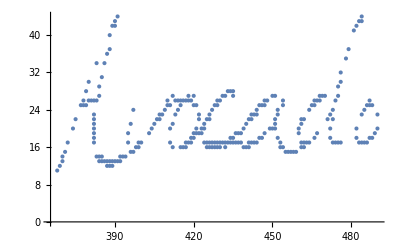

```mathematica
ListPlot[PixelValuePositions[ImageResize[-Graphics-,500],Black]]
```